```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*
(*Turns off blue and red*)
tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.0 π;
θ3=0.5π;
*)

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.5 π;
θ3=0.5π;

ϕ=0.5 π;
ϕ3=0;
```

```mathematica
ψA1L={};
ψAML={};
ψA2L={};
ψA3L={};

ψB1L={};
ψBML={};
ψB2L={};
ψB3L={};


For[θM=0,θM≤2 π,θM+=0.1,
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];

{e,ψ}=Transpose[Sort[Transpose[Eigensystem[Hsp,-10]]]];



n=5;
Print[{θM,e[[n]],e[[n-1]]}];
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];




e[[n-1]];
ψB1ue=Table[{i-1,Abs[ψ[[n-1,i]]]},{i,1,Nx}];
ψBMue=Table[{i-1-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx,4Nx+NxM}];
ψB2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψB3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];

ψA1L=Join[ψA1L,{ψA1ue}];
ψAML=Join[ψAML,{ψAMue}];
ψA2L=Join[ψA2L,{ψA2ue}];
ψA3L=Join[ψA3L,{ψA3ue}];

ψB1L=Join[ψB1L,{ψB1ue}];
ψBML=Join[ψBML,{ψBMue}];
ψB2L=Join[ψB2L,{ψB2ue}];
ψB3L=Join[ψB3L,{ψB3ue}];

];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{0,-3.82537×10^-12,-8.83515×10^-7}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{0.1,-3.88233×10^-12,-2.68757×10^-8}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

{0.2,-3.85005×10^-12,-2.04012×10^-8}

{0.3,-3.70539×10^-12,-3.18839×10^-8}

{0.4,-3.46215×10^-12,-2.65424×10^-7}

{0.5,-3.16235×10^-12,-2.02004×10^-6}

{0.6,-2.85127×10^-12,-2.73218×10^-6}

{0.7,-2.55908×10^-12,-2.1504×10^-6}

{0.8,-2.30091×10^-12,-6.64591×10^-7}

{0.9,-2.07966×10^-12,-4.87245×10^-8}

{1.,-1.893×10^-12,-1.99255×10^-8}

{1.1,-1.73671×10^-12,-1.23865×10^-8}

{1.2,-1.60643×10^-12,-9.09188×10^-9}

{1.3,-1.49773×10^-12,-7.32119×10^-9}

{1.4,-1.40755×10^-12,-6.26457×10^-9}

{1.5,-1.33189×10^-12,-5.60266×10^-9}

{1.6,-1.26935×10^-12,-5.18818×10^-9}

{1.7,-1.21769×10^-12,-4.9476×10^-9}

{1.8,-1.17569×10^-12,-4.84468×10^-9}

{1.9,-1.14164×10^-12,-4.86597×10^-9}

{2.,-1.11535×10^-12,-5.01628×10^-9}

{2.1,-1.09521×10^-12,-5.32102×10^-9}

{2.2,-1.08138×10^-12,-5.83742×10^-9}

{2.3,-1.0735×10^-12,-6.68534×10^-9}

{2.4,-1.07133×10^-12,-8.13547×10^-9}

{2.5,-1.07377×10^-12,-1.09216×10^-8}

{2.6,-1.08205×10^-12,-1.79054×10^-8}

{2.7,-1.09553×10^-12,-6.04102×10^-8}

{2.8,-1.1149×10^-12,-2.27576×10^-6}

{2.9,-1.14052×10^-12,-6.01107×10^-6}

{3.,-1.17269×10^-12,-9.93775×10^-6}

{3.1,-1.21205×10^-12,-0.0000139784}

{3.2,-1.26×10^-12,-0.0000180583}

{3.3,-1.31726×10^-12,-0.0000220941}

{3.4,-1.38568×10^-12,-0.0000259912}

{3.5,-1.46697×10^-12,-0.0000296414}

{3.6,-1.56382×10^-12,-0.0000329202}

{3.7,-1.67996×10^-12,-0.0000356825}

{3.8,-1.81924×10^-12,-0.0000377561}

{3.9,-1.98692×10^-12,-0.0000389344}

{4.,-2.19027×10^-12,-0.0000389654}

{4.1,-2.43781×10^-12,-0.000037545}

{4.2,-2.73916×10^-12,-0.0000343239}

{4.3,-3.10395×10^-12,-0.0000289694}

{4.4,-3.53604×10^-12,-0.0000213759}

{4.5,-4.02243×10^-12,-0.0000121923}

{4.6,-4.51432×10^-12,-3.70229×10^-6}

{4.7,-4.91555×10^-12,-2.99104×10^-7}

{4.8,-5.11453×10^-12,-4.62463×10^-6}

{4.9,-5.06913×10^-12,-0.0000161447}

{5.,-4.84009×10^-12,-0.0000293898}

{5.1,-4.53142×10^-12,-0.0000401562}

{5.2,-4.22334×10^-12,-0.0000470643}

{5.3,-3.95541×10^-12,-0.0000503874}

{5.4,-3.74256×10^-12,-0.0000508479}

{5.5,-3.5857×10^-12,-0.0000491112}

{5.6,-3.48206×10^-12,-0.0000456748}

{5.7,-3.42769×10^-12,-0.0000408892}

{5.8,-3.41926×10^-12,-0.0000350084}

{5.9,-3.4532×10^-12,-0.0000282462}

{6.,-3.52484×10^-12,-0.0000208472}

{6.1,-3.62583×10^-12,-0.0000131861}

{6.2,-3.74001×10^-12,-5.89884×10^-6}

```mathematica
1.2/π
```

0.381972

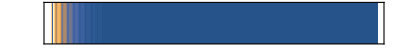

```mathematica
nt=48;
ψbar=Join[ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]]];
ψbarC=Join[Table[{i,0.0,ψbar[[i,2]]},{i,1,Length[ψbar]}],Table[{i,1.0,ψbar[[i,2]]},{i,1,Length[ψbar]}]];
bar=ListContourPlot[ψbarC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->1/10,FrameTicks->None]
```

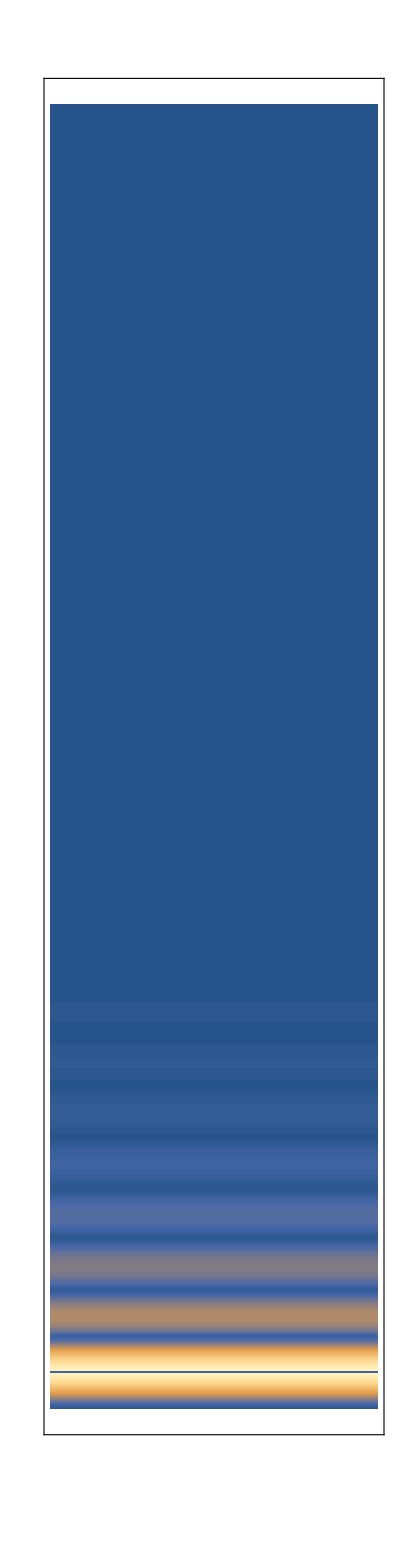

```mathematica
nt=48;
ψleg=ψA3L[[nt]];
ψlegC=Join[Table[{0.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}],Table[{1.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}]];
leg=ListContourPlot[ψlegC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->10/1,FrameTicks->None]
```

```mathematica
Manipulate[ListPlot[{ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]],ψA3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψA1L],1}]
```

```mathematica
Manipulate[ListPlot[{ψB1L[[nt]],ψBML[[nt]],ψB2L[[nt]],ψB3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψB1L],1}]
```